```mathematica
ClearAll["Global`*"]
$PlotTheme = "Monochrome";
```

Porovnání analytického výsledku s numerickým

```mathematica
a:=4;
b:=2;
c:=10
```

```mathematica
re=Rectangle[{0,0},{a,b}]
```

Rectangle[{0,0},{4,2}]

```mathematica
{RectangleEigenvalues,RectangleEigenvectors}=NDEigensystem[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈re,c];
```

```mathematica
{RectangleEigenvaluesFine,RectangleEigenvectorsFine}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},
u[x,y],
{x,y}∈re,
c, 
Method->{"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.3}}}}
];
```

```mathematica
N[NumericalSort[Flatten[Table[Pi^2*m^2/a^2+Pi^2*n^2/b^2,{m,1,c/2},{n,1,c/2}]]]]
RectangleEigenvalues
RectangleEigenvaluesFine
```

{3.08425,4.9348,8.01905,10.4865,12.337,12.337,15.4213,17.8887,19.7392,22.8235,24.674,25.2909,27.7583,32.0762,37.6279,40.0953,41.9458,45.0301,49.348,54.8997,62.3019,64.1524,67.2367,71.5546,77.1063}

{3.08426,4.93482,8.01915,10.4869,12.3374,12.3375,15.4218,17.8905,19.7401,22.8282}

{3.08554,4.9375,8.03514,10.5609,12.416,12.416,15.5288,18.167,19.9565,23.5646}

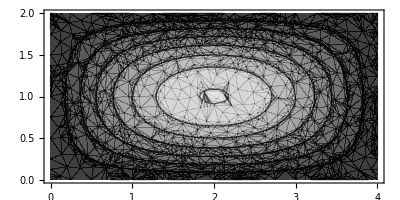
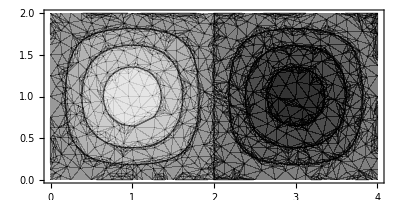
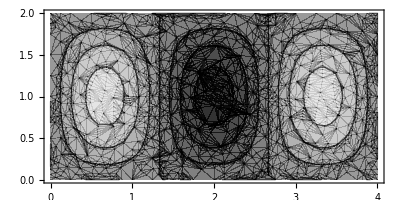
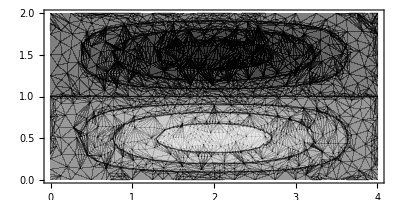
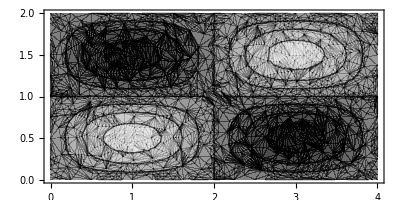
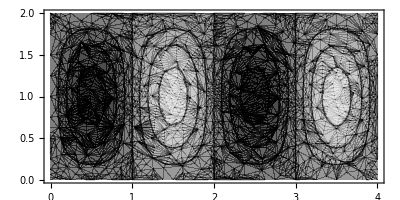
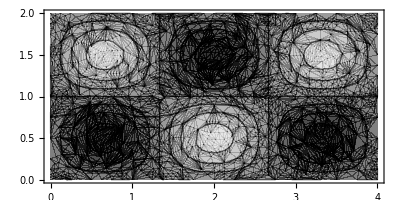
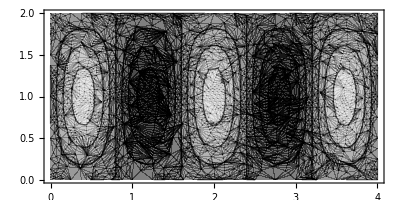

```mathematica
ContourPlot[#, {x, y} ∈re,AspectRatio->Automatic] & /@ RectangleEigenvectors
```